```mathematica
Data23F={
{33.7, -81.7, 22/8},
{34.9, -59.7, 22/8},
{33.7, -39.4, 21/8},
{34.8, -13.2, 21/8},
{33.3, 16.6, 20/8},
{34.6, 48.8, 20/8},
{33.1, 69.1, 19/8},
{34.4, 109.6, 19/8},
{33.1, 130.0, 18/8},
{34.4, 176.4, 18/8}};
```

```mathematica
Round[17/8//N,0.01]
```

2.12

```mathematica
Table[Round[i/j//N,0.01],{i,16,24},{j,9,3,-1}]
```

{{1.78,2.,2.29,2.67,3.2,4.,5.33},{1.89,2.12,2.43,2.83,3.4,4.25,5.67},{2.,2.25,2.57,3.,3.6,4.5,6.},{2.11,2.38,2.71,3.17,3.8,4.75,6.33},{2.22,2.5,2.86,3.33,4.,5.,6.67},{2.33,2.62,3.,3.5,4.2,5.25,7.},{2.44,2.75,3.14,3.67,4.4,5.5,7.33},{2.56,2.88,3.29,3.83,4.6,5.75,7.67},{2.67,3.,3.43,4.,4.8,6.,8.}}

```mathematica
Data25Fs0xtof={
{37.55,-58.9 , 22/8},
{38.18,-35.6, 22/8},
{38.71, -17.5, 22/8},
{37.64, 1.59, 21/8},
{38.2, 21.8, 21/8},
{38.8, 45.1, 21/8},
{37.6, 52.5, 20/8},
{38.1, 69.5, 20/8},
{38.6, 109.9, 20/8},
{37.7, -116.2, 23/8},
{38.2,-92.9, 23/8},
{38.8, -75.9, 23/8}
};
```

```mathematica
Data25F={
{37.7, 21.7/8, 22/8},
{38.2, 22.0/8, 22/8},
{38.7, 22.3/8, 22/8},
{37.6, 20.8/8, 21/8},
{38.2, 21.0/8, 21/8},
{38.7, 21.3/8, 21/8},
{37.5, 19.9/8, 20/8},
{37.9, 20.1/8, 20/8},
{38.5, 20.3/8, 20/8},
{37.7, 22.7/8, 23/8},
{38.3, 23.1/8, 23/8},
{38.8, 23.4/8, 23/8}
};
```

{37,39}

{2,3}

{-0.0676409,2.41191,1.06027}

2.41191-0.0676409 t+1.06027 x

fit least-square = 0.00102571

{2.73782,2.75}

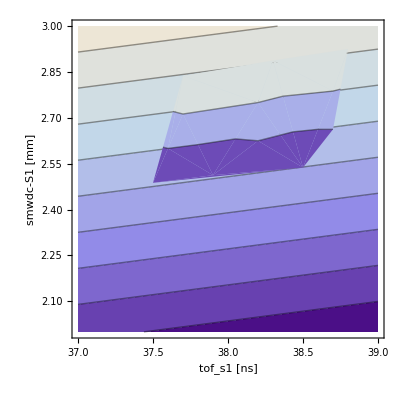

```mathematica
Data=Data25F;
nParT =1;
nParX =2 ;(* including constant*)
(*----------------------------------*)
rangeT={Floor[Min[Transpose[Data][[1]]]],Ceiling[Max[Transpose[Data][[1]]]]}
rangeX={Round[Floor[Min[Transpose[Data][[2]]]],1],Round[Ceiling[Max[Transpose[Data][[2]]]],1]}
fitPar=Join[Array[parT,nParT],Array[parX,nParX,0]];
par=fitPar/.FindFit[Data,Sum[parT[i] t^i,{i,1,nParT}]+ Sum[parX[i] x^i,{i,0,nParX-1}], fitPar,{t,x}]
fit[t_,x_]:=Sum[par[[i]] t^i,{i,1,nParT}]+Sum[par[[i+1+nParT]] x^i,{i,0,nParX-1}]
fit[t,x]
"fit least-square = "<>ToString[Sum[(Data[[i,3]]-fit[Data[[i,1]],Data[[i,2]]])^2, {i, 1, Length[Data]}]]
{fit[Data[[1,1]],Data[[1,2]]],Data[[1,3]]//N}
Show[{
ContourPlot[fit[t,x], {t, rangeT[[1]],rangeT[[2]]}, {x, rangeX[[1]],rangeX[[2]]},Contours->Table[i/8,{i,16,30}], FrameLabel->{"tof_s1 [ns]", "smwdc-S1 [mm]"}],
ListContourPlot[Data,Contours->Table[i/8,{i,16,28}]]
}]
```

```mathematica
Data={
{-32.5, -84.2, -77.52},
{-9.48, -75.8, -77.52},
{14.9, -70.8, -77.52},

{-39.4,-18.8, -23.83},
{-10.4, -17.1, -23.83},
{26.15,23.8,-23.83},

{-35.9, 46.6, 29.9},
{-3.16, 31.54, 29.9},
{27.3,19.8,29.9},

{33.6, 112.1, 83.6},
{-5.46,90.27, 83.6},
{22.7, 63.42, 83.6},

{-27.0, 190.9,147.31},
{2.87, 155.7, 147.31},
{26.7,108.7,147.31},

{-28.2,291.6,219.5},
{28.2,160.7,219.5}};
```

```mathematica
p1=0;
{p0,p1,p2, p3,p4,p5, p6}={a1,a2,a3,a4,a5,a6,a7}/.FindFit[Data,a1 t +a2 t^2+ a3 t^3 + a4 x+a5 x^2+a6 x^3 + a7, {a1,a2, a3, a4,a5, a6,a7},{t,x}]
fit[t_,x_]:=p0 t +p1 t^2+p2 t^3+p3 x+p4 x^2+p5 x^3+p6;
Sum[h=Data[[i,1]];k=Data[[i,2]];(Data[[i,3]]-fit[h,k])^2, {i, 1, Length[Data]}]
{fit[Data[[1,1]],Data[[1,2]]],Data[[1,3]]//N}
```

{1.39421,-0.0086466,-0.00116198,1.00608,0.00210031,-9.06047×10^-6,-10.5369}

8273.53

{-89.5062,-77.52}

```mathematica
p1=0;
{p0,p1}={a1,a2}/.FindFit[Data,(x + a1 a2 t)/(1+ a1 t), {a1,a2},{t,x}]
fit[t_,x_]:=(x + p0 p1 t)/(1+ p0 t);
Sum[h=Data[[i,1]];k=Data[[i,2]];(Data[[i,3]]-fit[h,k])^2, {i, 1, Length[Data]}]
{fit[Data[[1,1]],Data[[1,2]]],Data[[1,3]]//N}
```

{33.3012,53.7906}

155333.

{53.9182,-77.52}